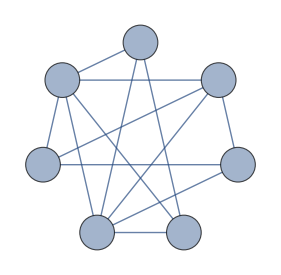

```mathematica
(*1. Задать списки дуг и узлов графа. Используя функцию Graph построить заданный ориентированный граф с использованием стилей (согласно лекции).*)

v = Range[7];
e = {1-> 2, 3-> 1, 1-> 4, 5-> 2, 1-> 6, 3-> 6, 3-> 7, 4-> 3, 5-> 3, 5-> 6, 6-> 2, 7-> 1, 7-> 4};
Graph[e, GraphLayout->"CircularEmbedding", VertexLabels->Placed["Name",Center], VertexSize->0.4, VertexLabelStyle-> Directive[Italic, 28], EdgeShapeFunction->GraphElementData["FilledArrow","ArrowSize"->0.05], EdgeStyle->Thick]
```

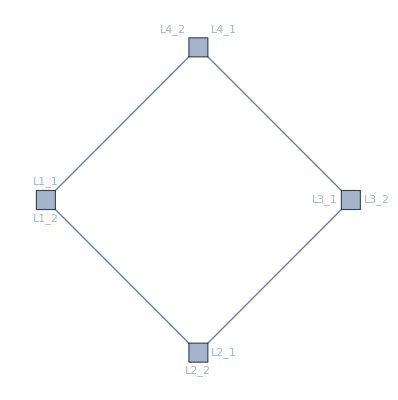

```mathematica
(*2 Изобразить граф на рисунке: *)
Graph[{Labeled[1,Placed[{"L1_1","L1_2"},{Above,Below}]],Labeled[2,Placed[{"L2_1","L2_2"},{After,Below}]],
Labeled[3,Placed[{"L3_1","L3_2"},{Before,After}]],Labeled[4,Placed[{"L4_1","L4_2"},{{Above,After},{Above,Before}}]]},
{1<-> 2,2<->3,3<->4,4<->1},VertexSize->Small, VertexShapeFunction->"Square"]
```

```mathematica
(*3. Изобразить графы как на рисунке в виде списка. У всех графов списка есть общее свойство, принимающее разные значения и поволяющее объединить графы в список (функция Table).*)
```


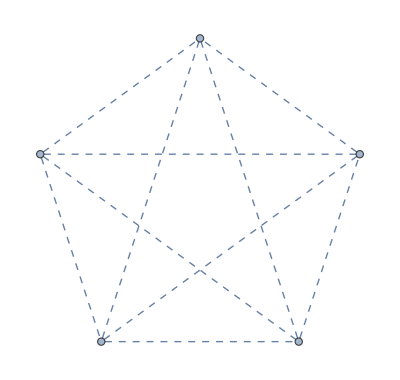
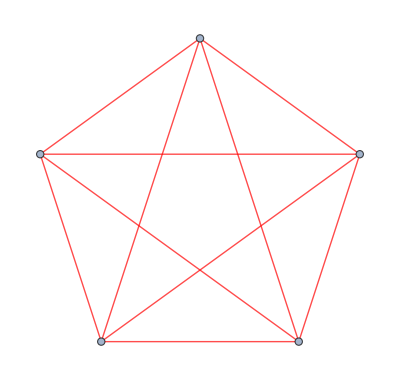

```mathematica
e={1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5};
Table[Graph[e,EdgeStyle->s],{s,{Thick, Dashed, Red}}]
```

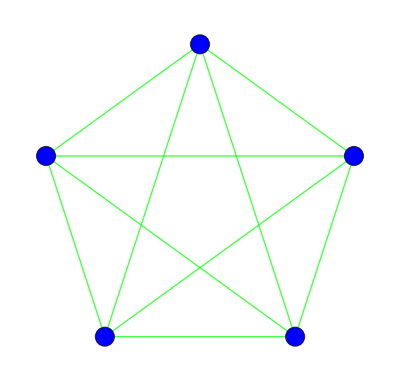
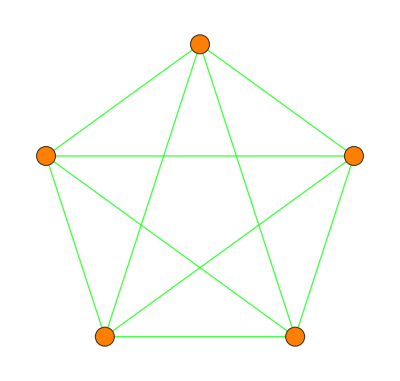
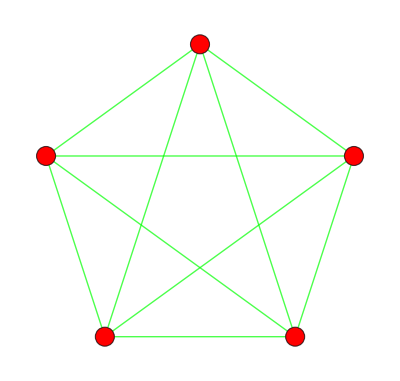

```mathematica
(*4. Изобразить графы как на рисунке в виде списка. У всех графов списка есть общее свойство,принимающее разные значения и позволяющее объединить графы в список (функция Table).*)
Table[Graph[e,VertexSize->Small,VertexStyle->s,EdgeStyle->Green],{s,{Blue, Orange, Red}}]
```

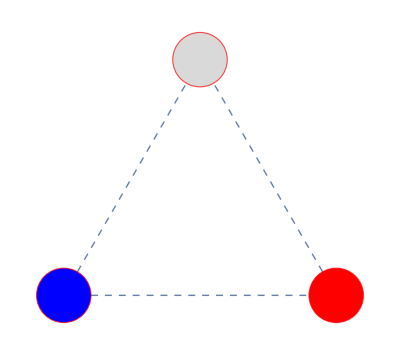
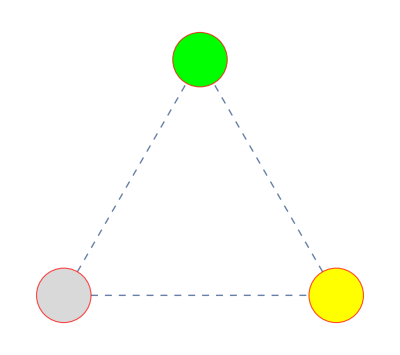
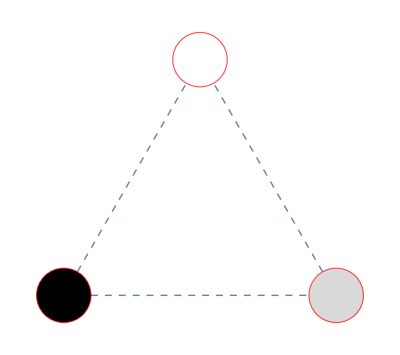

```mathematica
(*5. Изобразить графы как на рисунке в виде списка. У всех графов списка есть общее свойство,принимающее разные значения и позволяющее объединить графы в список (функция Table).*)
e={1<->2,1<->3,2<->3};
Table[Graph[e,VertexSize->Medium,VertexStyle->s,EdgeStyle->Dashed, BaseStyle->Directive[EdgeForm[Red], EdgeForm[Thick]]],
{s,{{1->Blue,2->Red,3->LightGray}, 
{1->LightGray,2->Yellow,3->Green},
 {1->Black,2->LightGray,3->White}}}]
```

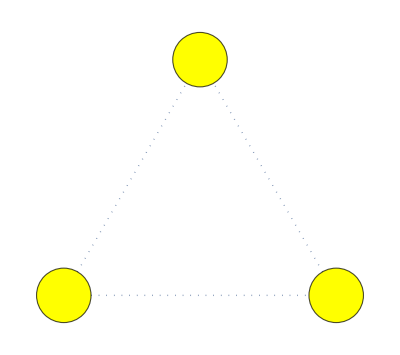
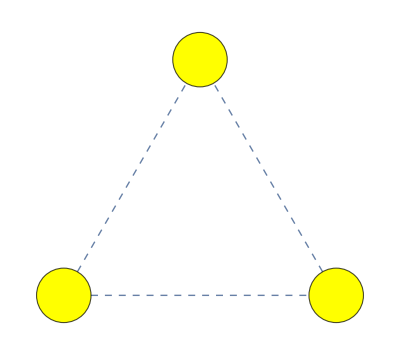
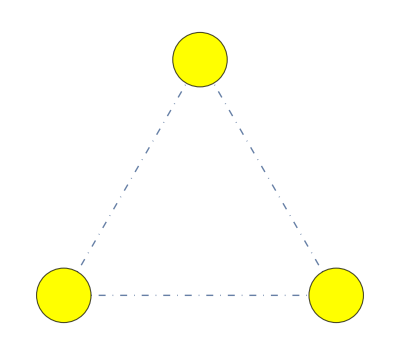

```mathematica
(*6. Изобразить графы как на рисунке в виде списка. У всех графов списка есть общее свойство,принимающее разные значения и позволяющее объединить графы в список (функция Table).*)
Table[Graph[{1<->2,1<->3,2<->3},VertexSize->Medium,VertexStyle->Directive[Yellow,EdgeForm[s]],EdgeStyle->s],
{s,{Dotted,Dashed,DotDashed}}]
```

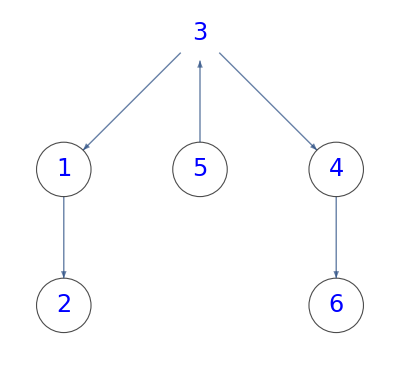

```mathematica
(*7. Построить ациклический граф (граф без циклов),содержащий 6 вершин.Отобразить его как на картинке,используя соответсвующий layout. Корневую вершину отобразить в виде произвольного изображения.*)
Graph[{3->4,3->1,5->3,1->2,4->6},VertexSize->Large,VertexStyle->White,VertexLabels -> Placed["Name", Center],VertexLabelStyle->Directive[Blue,Italic,24],GraphLayout->{"LayeredDigraphEmbedding","RootVertex"->3},VertexShape->{3->-Graphics-}]
```

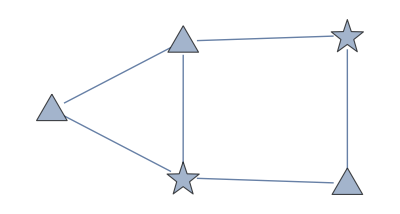

```mathematica
(*8. Изобразить произвольный граф. Четные вершины изобразить в виде звезды,нечетные в виде треугольника (используя тестирующую функцию).*)
e={5<->2,1<->2,1<->4,3<->4,3<->5,2<->3};
Graph[e,VertexSize->Medium,VertexShapeFunction->{_?EvenQ->"Star",_?OddQ->"Triangle"}]
```

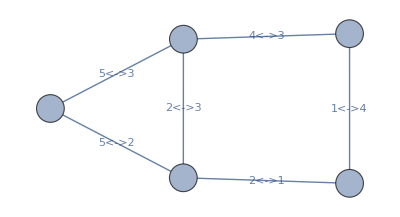

```mathematica
(*9. Изобразить произвольный граф. На графе отобразить метки ребер в виде имени ребра.*)
Graph[e, VertexSize->Medium, EdgeLabels->Placed["Name", Center]]
```

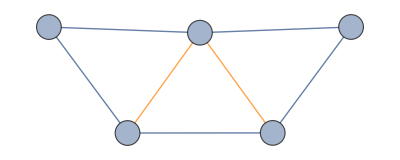

```mathematica
(*10. Изобразить произвольный ориентированный граф. На графе отобразить другим цветом дуги,которые исходят из заданной вершины (используя шаблон (без использования свойства GraphHighlight)).*)
Graph[{4->5,5->3,2->3,1->2,4->1,3->4,3->1},VertexSize->Medium,VertexLabels -> Placed["Name", Center],EdgeShapeFunction->"FilledArrow",EdgeStyle->{3->_-> Orange}]
```

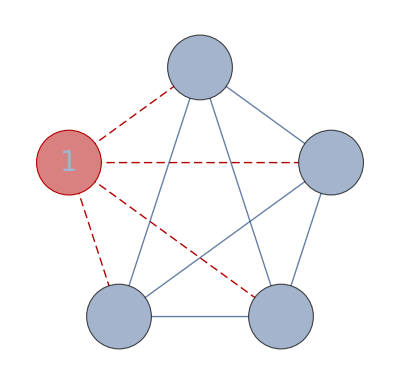

```mathematica
(*11. Изобразить полный ориентированный граф на 5 вершинах. Выделить произвольную вершину и все входящие в нее дуги (с использованием шаблона). Выделенные дуги отобразить прерывистой линией (GraphHighlightStyle). Выделение провести двумя способами,используя:
-свойство GraphHighlight;
 -функцию HighlightGraph.*)
CompleteGraph[5,VertexSize->Large,VertexLabelStyle->Directive[Italic,28],VertexLabels -> Placed["Name", Center],EdgeShapeFunction->"FilledArrow",GraphHighlight->{1,1<->_},GraphHighlightStyle->"Dashed"]
```

```mathematica
HighlightGraph[CompleteGraph[5,VertexSize->Large,VertexLabelStyle->Directive[Italic,28],VertexLabels -> Placed["Name", Center],EdgeShapeFunction->"FilledArrow"],{1,1<->_},GraphHighlightStyle->"Dashed"]
```

-Graphics-

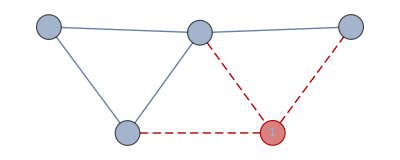

```mathematica
Graph[{4->5,5->3,2->3,1->2,4->1,3->4,3->1},VertexSize->Medium,VertexLabels -> Placed["Name", Center],EdgeShapeFunction->"FilledArrow",GraphHighlight->{1,1->_,_->1},GraphHighlightStyle->"Dashed"]
```

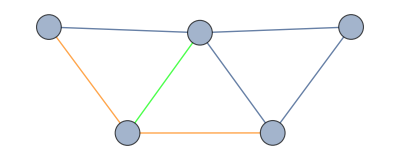

```mathematica
Graph[{4->5,5->3,2->3,1->2,4->1,3->4,3->1},VertexSize->Medium,VertexLabels -> Placed["Name", Center],EdgeShapeFunction->"FilledArrow",EdgeStyle->{4->_-> Orange, 3->4->Green}]
```

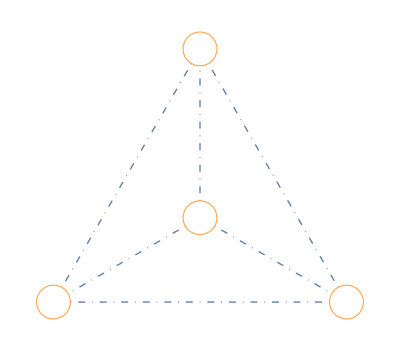

```mathematica
CompleteGraph[4,VertexSize->Medium,VertexStyle->White,EdgeStyle->DotDashed,  BaseStyle->Directive[EdgeForm[Orange], EdgeForm[Thick],EdgeForm[Dashed]]]
```

```mathematica
Graph[{Directive[1<->2, Orange],2<->3,3<->4,4<->1},BaseStyle->Thick]
```

Graph[{Directive[1<->2,RGBColor[1, 0.5, 0]],2<->3,3<->4,4<->1},BaseStyle→Thickness[Large]]

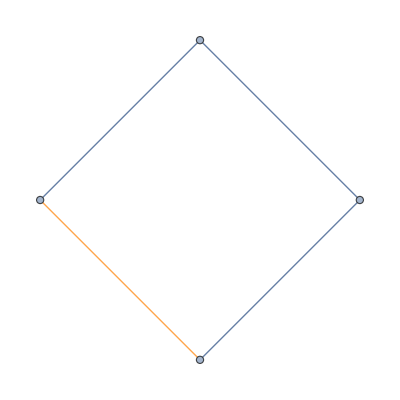

```mathematica
Graph[{1<->2,2<->3,3<->4,4<->1},BaseStyle->Thick, EdgeStyle->{1<->2->Orange}]
```

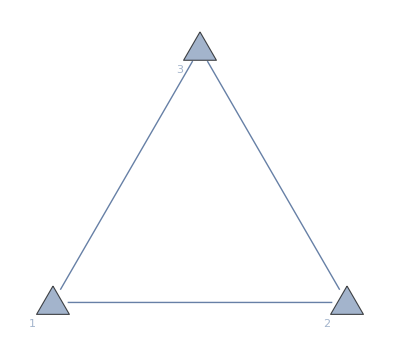

```mathematica
Graph[{1<->2,2<->3,3<->1},VertexSize->Small,VertexShapeFunction->"Triangle",VertexLabels->Placed[{"Name","Name"},{Center,{Below,Before}}]]
```

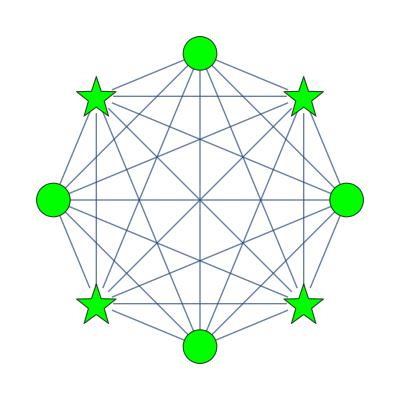

```mathematica
CompleteGraph[8,VertexSize->0.3,VertexStyle->Directive[Green],VertexShapeFunction->{_?OddQ->"Star"}]
```

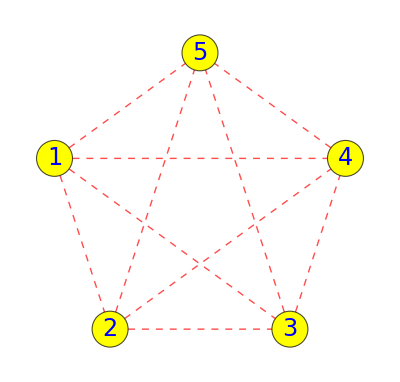

```mathematica
CompleteGraph[5,VertexSize->Medium,VertexStyle->Directive[Yellow],EdgeStyle->Directive[Dashed,Red,Thick],VertexLabels->Placed["Name",Center],VertexLabelStyle->Directive[Blue,Italic,24]]
```